```mathematica
Quit[];
```

```mathematica
(* This is a companion Mathematica notebook for https://arxiv.org/abs/2610.XXXXX *)
(* The latest version of this notebook is hosted at https://github.com/PhysicsBaker/Practical-Guide-to-Sensitivity-Projections *)
(* Since variable names are reused, please run the Quit[]; cell at the start of each section*)
```

## 2 Executive Summary

```mathematica
(*2.2*)
FindRoot[1/2 Erfc[√(χ2t/2)]==0.05,{χ2t,3}]
(*2.3*)
FindRoot[1/2 Erfc[√(χ2t/2)]==0.025,{χ2t,3}]
```

{χ2t→2.70554}

{χ2t→3.84146}

## 3 Poisson Distributed Data

```mathematica
(* Please run this cell before beginning this section so that variables are not inadvertantly stored from previous sections *)
Quit[];
```

```mathematica
(*3.1*)
HSM={11,14};
(*3.2*)
HBSM={15,22};
```

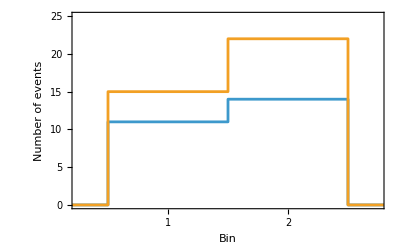

```mathematica
(*Figure 1*)
ListStepPlot[{{{0,0},{1,HSM[[1]]},{2,HSM[[2]]},{3,0}},{{0,0},{1,HBSM[[1]]},{2,HBSM[[2]]},{3,0}}},
Center,FrameLabel->{"Bin","Number of events"},FrameTicks->{{Automatic,None},{{1,2},None}},
PlotRange->{{0.25,2.75},{0,25}},
Frame->True]
```

### 3.1 Exact p-value

```mathematica
o={12,20};
```

```mathematica
(*3.4*)
(HBSM[[1]]^o[[1]] Exp[-HBSM[[1]]])/(o[[1]]!)//N
```

0.0828592

```mathematica
(*3.6*)
Product[(HBSM[[i]]^o[[i]] Exp[-HBSM[[i]]])/(o[[i]]!),{i,1,Length[HBSM]}]//N
```

0.0067018

```mathematica
(*3.7*)
Po[o_]:=Product[(HBSM[[i]]^o[[i]] Exp[-HBSM[[i]]])/(o[[i]]!),{i,1,Length[HBSM]}]//N
```

```mathematica
(*3.8*)
A=HSM;
```

#### 3.1.1 Goodness of Fit

```mathematica
(*3.12*)
PA=Po[A]
```

0.00131966

```mathematica
(*3.16*)
Po[HBSM]
```

0.00867972

```mathematica
PTable=Flatten[Table[{i,j,Po[{i,j}]},{i,0,35},{j,0,35}],1];
```

```mathematica
PInt=Interpolation[PTable,InterpolationOrder->1];
```

```mathematica
(*Figure 2*)
Show[
Graphics[{PointSize[1/36],
MapThread[{#2,Point[#1]}&,{PTable[[All,1;;2]],ColorData["Rainbow"]/@Rescale[PTable[[All,3]]]}]},
PlotRange->All,Axes->True,Frame->True,FrameLabel->{"o_1","o_2"}],
ContourPlot[PInt[i,j]==PA,{i,0,35},{j,0,35},ContourStyle->White,PlotLegends->BarLegend[{"Rainbow",{0,PTable[[563]][[3]]}},LegendLabel->"Probability P_P"]],
Graphics[{PointSize[1/36],
{{Black,Point[{15,22}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][1],Point[{15,22}]}}}],
Graphics[{PointSize[1/36],
{{White,Point[{11,14}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][(PTable[[411]][[3]])/(PTable[[563]][[3]])],Point[{11,14}]}}}]
]
```

-Graphics-

```mathematica
(*3.19*)
1-Sum[If[PTable[[i]][[3]]>PA,PTable[[i]][[3]],0],{i,1,Length[PTable]}]
```

0.149445

#### 3.1.2 Hypothesis Test

```mathematica
(*3.24*)
qo[o_]:=-2Sum[o[[i]]Log[HBSM[[i]]/HSM[[i]]]-HBSM[[i]]+HSM[[i]],{i,1,Length[HBSM]}]//N
```

```mathematica
(*3.26*)
qA=qo[A]
```

4.52101

```mathematica
PqTable=Flatten[Table[{i1,i2,Po[{i1,i2}],qo[{i1,i2}]},{i1,0,35},{i2,0,35}],1];
```

```mathematica
PInt2=Interpolation[PqTable[[All,{1,2,3}]],InterpolationOrder->1];
qInt2=Interpolation[PqTable[[All,{1,2,4}]],InterpolationOrder->1];
```

```mathematica
(* Figure 3 left*)
Show[
Graphics[{PointSize[1/36],
MapThread[{#2,Point[#1]}&,{PqTable[[All,1;;2]],ColorData["Rainbow"]/@Rescale[PqTable[[All,4]]]}]},
PlotRange->All,Axes->True,Frame->True,FrameLabel->{"o_1","o_2"}],
ContourPlot[qInt2[i,j]==qA,{i,0,35},{j,0,35},ContourStyle->Black,PlotLegends->BarLegend[{"Rainbow",{PqTable[[1296]][[4]],PqTable[[1]][[4]]}},LegendLabel->"Test statistic q"]],
Graphics[{PointSize[1/36],
{{Black,Point[{15,22}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][(PqTable[[1296]][[4]]-PqTable[[563]][[4]])/(PqTable[[1296]][[4]]-PqTable[[1]][[4]])],Point[{15,22}]}}}],
Graphics[{PointSize[1/36],
{{Gray,Point[{11,14}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][(PqTable[[1296]][[4]]-PqTable[[411]][[4]])/(PqTable[[1296]][[4]]-PqTable[[1]][[4]])],Point[{11,14}]}}}]
]
```

-Graphics-

```mathematica
(*Figure 3 right*)
Show[
Graphics[{PointSize[1/36],
MapThread[{#2,Point[#1]}&,{PTable[[All,1;;2]],ColorData["Rainbow"]/@Rescale[PTable[[All,3]]]}]},
PlotRange->All,Axes->True,Frame->True,FrameLabel->{"o_1","o_2"}],
ContourPlot[PInt[i,j]==PA,{i,0,35},{j,0,35},ContourStyle->White,PlotLegends->BarLegend[{"Rainbow",{0,PTable[[563]][[3]]}},LegendLabel->"Probability P_P"]],
ContourPlot[qInt2[i,j]==qA,{i,0,35},{j,0,35},ContourStyle->Black],
Graphics[{PointSize[1/36],
{{Black,Point[{15,22}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][1],Point[{15,22}]}}}],
Graphics[{PointSize[1/36],
{{Gray,Point[{11,14}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][(PTable[[411]][[3]])/(PTable[[563]][[3]])],Point[{11,14}]}}}]
]
```

-Graphics-

```mathematica
(*3.28*)
Sum[If[PqTable[[i]][[4]]>=qA,PqTable[[i]][[3]],0],{i,1,Length[PqTable]}]
```

0.0188798

### 3.2 Monte Carlo and Asymptotic Estimates of the p-value

#### 3.2.1 Goodness of Fit

Monte Carlo Methods

```mathematica
NMC=10000;
```

```mathematica
draws=Table[RandomVariate[PoissonDistribution[HBSM[[i]]]],{j,1,NMC},{i,1,Length[HBSM]}];
```

```mathematica
PTableMC=Table[Po[draws[[i]]],{i,1,NMC}];
```

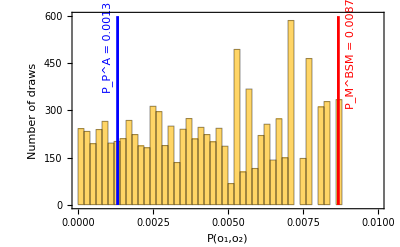

```mathematica
(*Figure 4 left*)
Show[Histogram[{PTableMC},{0.0002},PlotRange->{{0,0.01},{All,All}},Frame->True,FrameLabel->{"P(o_1,o_2)","Number of draws"}],
ParametricPlot[{Po[A],u},{u,-1,600},PlotStyle->Blue],
ParametricPlot[{Po[HBSM],u},{u,-1,600},PlotStyle->Red],
Epilog->{
Text[Style[Row[{Subsuperscript["P","P","A"]," = 0.0013"}],Blue],{0.001,500},{0,0},{0,1}],
Text[Style[Row[{Subsuperscript["P","M","BSM"]," = 0.0087"}],Red],{0.0091,480},{0,0},{0,1}]}]
```

```mathematica
(*3.31*)
Count[PTableMC,_?(Between[{0,Po[A]}])]
(*3.32*)
Count[PTableMC,_?(Between[{0,Po[A]}])]/NMC//N
```

1516

0.1516

```mathematica
(*3.33*)
qo2[o_]:=-2Sum[Log[HBSM[[j]]^o[[j]]/HBSM[[j]]^HBSM[[j]](HBSM[[j]]!)/(o[[j]]!)],{j,1,Length[HBSM]}]//N
```

```mathematica
(*3.35*)
qTableMC=Table[qo2[draws[[i]]],{i,1,NMC}];
```

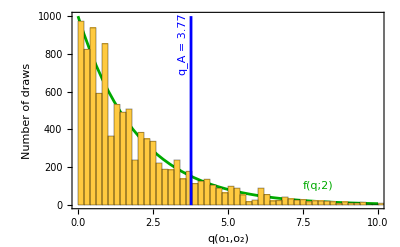

```mathematica
(*Figure 4 right *)
Show[Plot[NMC/5 PDF[ChiSquareDistribution[Length[HBSM]],x],{x,0,10},Frame->True,FrameLabel->{"q(o_1,o_2)","Number of draws"},PlotStyle->Darker@Green],
Histogram[qTableMC,{0.2},PlotRange->{{0,10},{All,All}}],
ParametricPlot[{qo2[A],u},{u,-1,1000},PlotStyle->Blue],
Epilog->{
Text[Style["q_A = 3.77",Blue],{3.5,850},{0,0},{0,1}],
Text[Style["f(q;2)",Darker@Green],{8,100},{0,0},{1,0}]}]
```

```mathematica
(*3.37*)
qo2[A]
```

3.76723

```mathematica
(*3.38*)
Count[qTableMC,_?(Between[{qo2[A],∞}])]
(*3.39*)
Count[qTableMC,_?(Between[{qo2[A],∞}])]/NMC//N
```

1516

0.1516

Asymptotic Distribution of the Test Statistic

```mathematica
(*3.44*)
Exp[-qo2[A]/2]
```

0.152039

Asymptotic Limit of the Test Statistic of the Asimov Data Set

```mathematica
(*3.55*)
χ2[H_,A_]:=Sum[(H[[i]]-A[[i]])^2/H[[i]],{i,1,Length[H]}]//N
```

```mathematica
(*3.56*)
χ2[HBSM,A]
```

3.97576

```mathematica
(*3.58*)
Exp[-χ2[HBSM,A]/2]
```

0.136986

#### 3.2.2 Hypothesis Test

Monte Carlo Methods

```mathematica
NMC=10000;
```

```mathematica
drawsBSM=Table[RandomVariate[PoissonDistribution[HBSM[[i]]]],{j,1,NMC},{i,1,Length[HBSM]}];
drawsSM=Table[RandomVariate[PoissonDistribution[HSM[[i]]]],{j,1,NMC},{i,1,Length[HSM]}];
```

```mathematica
qo3[o_]:=-2Sum[o[[i]]Log[HBSM[[i]]/HSM[[i]]]+HSM[[i]]-HBSM[[i]],{i,1,Length[HBSM]}]//N
```

```mathematica
(*3.61*)
qBSM=Table[qo3[drawsBSM[[j]]],{j,1,NMC}];
qSM=Table[qo3[drawsSM[[j]]],{j,1,NMC}];
```

```mathematica
(*3.63*)
qA = qo3[A]
```

4.52101

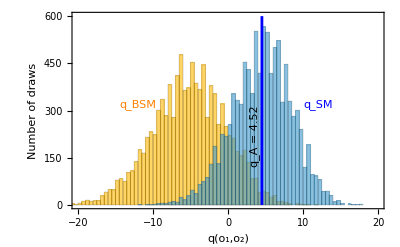

```mathematica
(*Figure 5*)
Show[Histogram[{qBSM,qSM},{0.5},Frame->True,PlotRange->{{-20,20},{All,All}},FrameLabel->{"q(o_1,o_2)","Number of draws"}],
ParametricPlot[{qA,u},{u,0,600},PlotStyle->Blue],
Epilog->{
Text["q_A = 4.52",{3.5,220},{0,0},{0,1}],
Text[Style["q_SM",Blue],{12,320},{0,0},{1,0}],
Text[Style["q_BSM",Orange],{-12,320},{0,0},{1,0}]}]
```

```mathematica
(*3.64*)
Count[qBSM,_?(Between[{qA,∞}])]
(*3.65*)
Count[qBSM,_?(Between[{qA,∞}])]/NMC//N
```

180

0.018

Wilks’ Theorem

```mathematica
(*3.66*)
H[μ_]:=μ HBSM + (1-μ)HSM
```

```mathematica
(*3.68*)
Timing[Monitor[qBSM=Table[FindMaximum[{-2Sum[drawsBSM[[j,i]]Log[HBSM[[i]]/(H[μ][[i]])]-HBSM[[i]]+H[μ][[i]],{i,1,Length[HBSM]}],0<=μ<=1},μ,PrecisionGoal->3][[1]],{j,1,NMC}];,{j}]]
```

{79.8967,Null}

```mathematica
(*3.72*)
qA = -2Sum[A⟦i⟧Log[HBSM⟦i⟧/A[[i]]]-HBSM⟦i⟧+A[[i]],{i,1,Length[HBSM]}]//N
```

4.52101

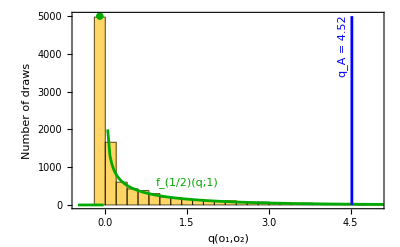

```mathematica
(*Figure 6*)
Show[
Histogram[{qBSM},{0.2},FrameLabel->{"q(o_1,o_2)","Number of draws"}],
Plot[{NMC/(2*5) PDF[ChiSquareDistribution[1],x]},{x,-0.5,100},PlotRange->{0,NMC/5},PlotStyle->Darker@Green],

ListPlot[{{-0.1,5000}},PlotStyle->Darker@Green],
ParametricPlot[{qo3[A],u},{u,0,NMC/2},PlotStyle->Blue],
Frame->True,PlotRange->{{-0.5,5},{All,All}},
Epilog->{
Text[Style["q_A = 4.52",Blue],{4.35,4200},{0,0},{0,1}],
Text[Style["f_(1/2)(q;1)",Darker@Green],{1.5,600},{0,0},{1,-0.4}]}]
```

```mathematica
(*3.73*)
Count[qBSM,_?(Between[{qA,∞}])]
(*3.74*)
Count[qBSM,_?(Between[{qA,∞}])]/NMC//N
```

163

0.0163

Asymptotic Distribution of the Test Statistic

```mathematica
(*3.83*)
Integrate[1/2 PDF[ChiSquareDistribution[1],x],{x,qA,∞}] //N
```

0.0167405

Asymptotic Limit of the Test Statistic of the Asimov Data Set

```mathematica
(*3.97*)
χ2[HBSM,A]
```

3.97576

```mathematica
(*3.102*)
1/2 Erfc[√(χ2[HBSM,A]/2)]
```

0.0230798

### 3.3 Realistic Example: Heavy Resonances at a Muon Collider

```mathematica
(*3.103*)
HSM={349,314,222,125,61,28};
(*3.104*)
HBSM={382,345,243,137,67,31};
```

```mathematica
(*3.105*)
A=HSM;
```

```mathematica
NMC=10000;
```

```mathematica
drawsBSM=Table[RandomVariate[PoissonDistribution[HBSM[[i]]]],{j,1,NMC},{i,1,Length[HBSM]}];
```

```mathematica
qTableMC=Table[qo2[drawsBSM[[i]]],{i,1,NMC}];
```

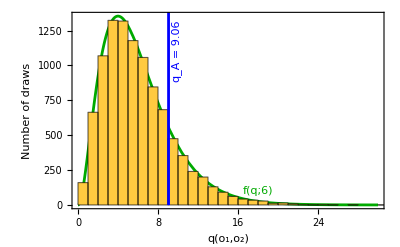

```mathematica
(*Figure 8 left *)
Show[Plot[NMC PDF[ChiSquareDistribution[Length[HBSM]],x],{x,0,30},Frame->True,FrameLabel->{"q(o_1,o_2)","Number of draws"},PlotStyle->Darker@Green],
Histogram[qTableMC,{1},PlotRange->{{0,10},{All,All}}],
ParametricPlot[{qo2[A],u},{u,-1,1400},PlotStyle->Blue],
Epilog->{
Text[Style["q_A = 9.06",Blue],{9.9,1100},{0,0},{0,1}],
Text[Style["f(q;6)",Darker@Green],{18,100},{0,0},{1,0}]}]
```

```mathematica
qo2[A]
```

9.05542

```mathematica
Count[qTableMC,_?(Between[{qo2[A],∞}])]
Count[qTableMC,_?(Between[{qo2[A],∞}])]/NMC//N
```

1665

0.1665

```mathematica
(*3.107*)
Integrate[PDF[ChiSquareDistribution[6],x],{x,qo2[A],∞}] //N
```

0.170485

```mathematica
χ2[HBSM,A]
```

9.32984

```mathematica
(*3.109*)
Integrate[PDF[ChiSquareDistribution[6],x],{x,χ2[HBSM,A],∞}] //N
```

0.15586

```mathematica
H[μ_]:=μ HBSM + (1-μ)HSM
```

```mathematica
Timing[Monitor[qBSM=Table[FindMaximum[{-2Sum[drawsBSM[[j,i]]Log[HBSM[[i]]/(H[μ][[i]])]-HBSM[[i]]+H[μ][[i]],{i,1,Length[HBSM]}],0<=μ<=1},μ,PrecisionGoal->3][[1]],{j,1,NMC}];,{j}]]
```

{80.3199,Null}

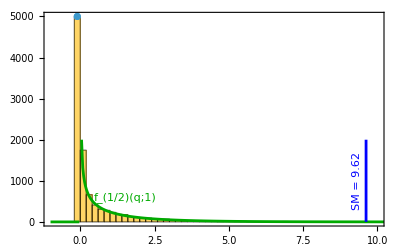

```mathematica
(*Figure 8 right*)
Show[
Histogram[{qBSM},{0.2}],
Plot[{NMC/(2*5) PDF[ChiSquareDistribution[1],x]},{x,-1,100},PlotRange->{0,NMC/5},PlotStyle->Darker@Green],

ListPlot[{{-0.1,5000}}],
ParametricPlot[{qo3[A],u},{u,0,NMC/5},PlotStyle->Blue],
Frame->True,PlotRange->{{-1,10},{All,All}},
Epilog->{Text[Style["SM = 9.62",Blue],{9.3,1000},{0,0},{0,1}],Text[Style["f_(1/2)(q;1)",Darker@Green],{1.5,600},{0,0},{1,-0.4}]}]
```

```mathematica
qo3[A]
```

9.61648

```mathematica
Count[qBSM,_?(Between[{qo3[A],∞}])]
Count[qBSM,_?(Between[{qo3[A],∞}])]/NMC//N
```

7

0.0007

```mathematica
(*3.111*)
Integrate[1/2 PDF[ChiSquareDistribution[1],x],{x,qo3[A],∞}] //N
```

0.000964196

```mathematica
χ2[HBSM,A]
```

9.32984

```mathematica
(*3.113*)
Integrate[1/2 PDF[ChiSquareDistribution[1],x],{x,χ2[HBSM,A],∞}] //N
```

0.00112726

## 4 Multinomially Distributed Data

```mathematica
(* Please run this cell before beginning this section so that variables are not inadvertantly stored from previous sections *)
Quit[];
```

```mathematica
(*4.1*)
HSM={10,12,12};
(*4.2*)
HBSM={13,14,7};
```

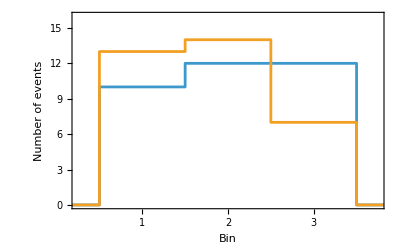

```mathematica
(*Figure 10*)
ListStepPlot[{{{0,0},{1,HSM[[1]]},{2,HSM[[2]]},{3,HSM[[3]]},{4,0}},{{0,0},{1,HBSM[[1]]},{2,HBSM[[2]]},{3,HBSM[[3]]},{4,0}}},
Center,FrameLabel->{"Bin","Number of events"},FrameTicks->{{Automatic,None},{{1,2,3},None}},
PlotRange->{{0.25,3.75},{0,16}},
Frame->True]
```

### 4.1 Exact p-value

```mathematica
A=HSM;
```

```mathematica
Ntotal=Total[A];
```

```mathematica
(*4.5*)
Po[o_]:=Ntotal! Product[1/(o[[i]]!) (HBSM[[i]]/Ntotal)^o[[i]],{i,1,Length[HBSM]}]//N
```

#### 4.1.1 Goodness of Fit

```mathematica
(*4.8*)
PA=Po[A]
```

0.0032628

```mathematica
(*4.11*)
PBSM=Po[HBSM]
```

0.0254393

```mathematica
(* The number of ways of of placing 𝑁 balls into 𝑀 bins is *)
numberOfWays[n_,m_]:=Binomial[n+m-1,n]

PossibilitiesModule[photons_,bins_]:=Module[{unpermutedPossibilities},unpermutedPossibilities=IntegerPartitions[photons,{bins},Range[0,photons]];
Flatten[Table[Permutations[unpermutedPossibilities[[i]]],{i,1,Length[unpermutedPossibilities]}],1]]
```

```mathematica
Possibilities=PossibilitiesModule[Ntotal,3];
```

```mathematica
PqTableM=Table[{Possibilities[[i]][[1]],Possibilities[[i]][[2]],Ntotal!Product[(HBSM[[j]]/Ntotal)^Possibilities[[i,j]] 1/(Possibilities[[i,j]]!),{j,1,3}]//N,-2Sum[Possibilities[[i,j]]Log[HBSM[[j]]/A[[j]]],{j,1,3}]},{i,1,Length[Possibilities]}];
```

```mathematica
PInt=Interpolation[PqTableM[[All,{1,2,3}]],InterpolationOrder->1]
qInt=Interpolation[PqTableM[[All,{1,2,4}]],InterpolationOrder->1]
```

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[…]

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[…]

```mathematica
qobs=-2Sum[A[[i]]Log[HBSM[[i]]/A[[i]]],{i,1,3}]//N
```

3.98901

```mathematica
(*Figure 11 left*)
Show[
Graphics[{PointSize[1/36],
MapThread[{#2,Point[#1]}&,{PqTableM[[All,1;;2]],ColorData["Rainbow"]/@Rescale[PqTableM[[All,3]]]}]},
PlotRange->All,Axes->True,Frame->True,FrameLabel->{"o_1","o_2"}],
ContourPlot[PInt[i,j]==PA,{i,0,35},{j,0,35},ContourStyle->White,
PlotLegends->BarLegend[{"Rainbow",{0,PqTableM[[591]][[3]]}},LegendLabel->"Probability P_P"]],ContourPlot[qInt[i,j]==qobs,{i,0,35},{j,0,35},ContourStyle->Black],
Graphics[{PointSize[1/36],
{{Black,Point[{13,14}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][1],Point[{13,14}]}}}],
Graphics[{PointSize[1/36],
{{White,Point[{10,12}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][(PqTableM[[627]][[3]])/(PqTableM[[591]][[3]])],Point[{10,12}]}}}]
]
```

-Graphics-

```mathematica
(*Figure 11 right*)
Show[
Graphics[{PointSize[1/36],
MapThread[{#2,Point[#1]}&,{PqTableM[[All,1;;2]],ColorData["Rainbow"]/@Rescale[PqTableM[[All,4]]]}]},
PlotRange->All,Axes->True,Frame->True,FrameLabel->{"o_1","o_2"}],ContourPlot[qInt[i,j]==qobs,{i,0,35},{j,0,35},ContourStyle->Black,PlotLegends->BarLegend[{"Rainbow",{Min[PqTableM[[All,4]]],Max[PqTableM[[All,4]]]}},LegendLabel->"Test statistic q"]],
Graphics[{PointSize[1/36],
{{Black,Point[{13,14}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][(PqTableM[[591]][[4]]-Min[PqTableM[[All,4]]])/(Max[PqTableM[[All,4]]]-Min[PqTableM[[All,4]]])],Point[{13,14}]}}}],
Graphics[{PointSize[1/36],
{{White,Point[{10,12}]}}}],
Graphics[{PointSize[0.015],
{{ColorData["Rainbow"][(PqTableM[[627]][[4]]-Min[PqTableM[[All,4]]])/(Max[PqTableM[[All,4]]]-Min[PqTableM[[All,4]]])],Point[{10,12}]}}}]
]
```

-Graphics-

```mathematica
(*4.13*)
Sum[If[PqTableM[[i,3]]<=PA,PqTableM[[i,3]],0],{i,1,Length[PqTableM]}]
```

0.122634

#### 4.1.2 Hypothesis Test

```mathematica
(*4.16*)
qobs=-2Sum[A[[i]]Log[HBSM[[i]]/A[[i]]],{i,1,3}]//N
```

3.98901

```mathematica
(*4.18*)
Sum[If[PqTableM[[i,4]]>=qobs,PqTableM[[i,3]],0],{i,1,Length[PqTableM]}]
```

0.0235097

### 4.2 Monte Carlo and Asymptotic Estimates of the p-value

#### 4.2.1 Goodness of Fit

Monte Carlo Methods

```mathematica
NMC=10000;
```

```mathematica
draws=Table[RandomVariate[MultinomialDistribution[Ntotal,HBSM/Ntotal]],{i,1,NMC}];
```

```mathematica
PTableMC=Table[Po[draws[[i]]],{i,1,NMC}];
```

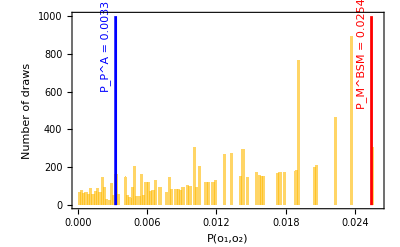

```mathematica
(*Figure 12 left*)
Show[Histogram[{PTableMC},{0.0002},PlotRange->{{0,0.026},{0,1000}},Frame->True,FrameLabel->{"P(o_1,o_2)","Number of draws"}],
ParametricPlot[{Po[A],u},{u,-1,1000},PlotStyle->Blue],
ParametricPlot[{Po[HBSM],u},{u,-1,1000},PlotStyle->Red],
Epilog->{
Text[Style[Row[{Subsuperscript["P","P","A"]," = 0.0033"}],Blue],{0.0024,840},{0,0},{0,1}],
Text[Style[Row[{Subsuperscript["P","M","BSM"]," = 0.0254"}],Red],{0.0246,800},{0,0},{0,1}]}]
```

```mathematica
(*4.21*)
Count[PTableMC,_?(Between[{0,Po[A]}])]
(*4.22*)
Count[PTableMC,_?(Between[{0,Po[A]}])]/NMC//N
```

1210

0.121

```mathematica
(*4.24*)
qo2[o_]:=-2Log[Product[(HBSM[[i]]/Ntotal)^o[[i]]/(HBSM[[i]]/Ntotal)^HBSM[[i]] (HBSM[[i]]!)/(o[[i]]!),{i,1,Length[HBSM]}]]//N
```

```mathematica
(*4.25*)
qTableMC=Table[qo2[draws[[i]]],{i,1,NMC}];
```

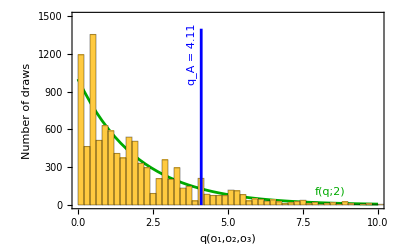

```mathematica
(*Figure 12 right *)
Show[Plot[NMC/5 PDF[ChiSquareDistribution[Length[HBSM]-1],x],{x,0,10},Frame->True,FrameLabel->{"q(o_1,o_2,o_3)","Number of draws"},PlotRange->{{0,10},{0,1500}},PlotStyle->Darker@Green],
Histogram[qTableMC,{0.2},PlotRange->{{0,10},{All,All}}],
ParametricPlot[{qo2[A],u},{u,-1,1400},PlotStyle->Blue],
Epilog->{
Text[Style["q_A = 4.11",Blue],{3.8,1200},{0,0},{0,1}],
Text[Style["f(q;2)",Darker@Green],{8.4,100},{0,0},{1,0}]}]
```

```mathematica
(*4.27*)
qo2[A]
```

4.10741

```mathematica
(*4.28*)
Count[qTableMC,_?(Between[{qo2[A],∞}])]
(*4.29*)
Count[qTableMC,_?(Between[{qo2[A],∞}])]/NMC//N
```

1210

0.121

Asymptotic Distribution of the Test Statistic

```mathematica
(*4.32*)
Exp[-qo2[A]/2]
```

0.128259

Asymptotic Limit of the Test Statistic of the Asimov Data Set

```mathematica
(*4.44*)
χ2[H_,A_]:=Sum[(H[[i]]-A[[i]])^2/H[[i]],{i,1,Length[H]}]//N
```

```mathematica
(*4.45*)
χ2[HBSM,A]
```

4.54945

```mathematica
(*4.47*)
Exp[-χ2[HBSM,A]/2]
```

0.102825

The G-test

```mathematica
(*4.51*)
PGo[o_]:=-2 Sum[o[[i]] Log[HBSM[[i]]/Max[o[[i]],10^-10]],{i,1,Length[HBSM]}]//N
```

```mathematica
(*4.53*)
```

```mathematica
PGo[A]
```

3.98901

```mathematica
qTableMCG=Table[PGo[draws[[i]]],{i,1,NMC}];
```

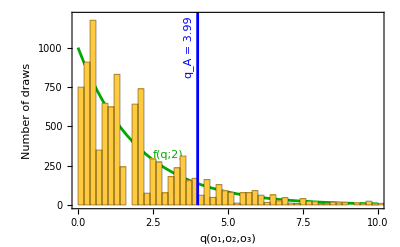

```mathematica
(*Figure 13*)
Show[Plot[NMC/5 PDF[ChiSquareDistribution[Length[HBSM]-1],x],{x,0,10},Frame->True,FrameLabel->{"q(o_1,o_2,o_3)","Number of draws"},PlotRange->{{0,10},{0,1200}},PlotStyle->Darker@Green],
Histogram[qTableMCG,{0.2},PlotRange->{{0,10},{All,All}}],
ParametricPlot[{PGo[A],u},{u,-1,1400},PlotStyle->Blue],
Epilog->{
Text[Style["q_A = 3.99",Blue],{3.7,1000},{0,0},{0,1}],
Text[Style["f(q;2)",Darker@Green],{3,320},{0,0},{1,-0.6}]}]
```

```mathematica
(*4.54*)
Count[qTableMCG,_?(Between[{PGo[A],∞}])]
(*4.55*)
Count[qTableMCG,_?(Between[{PGo[A],∞}])]/NMC//N
```

1368

0.1368

```mathematica
(*4.57*)
Exp[-PGo[A]/2]
```

0.136081

```mathematica
(*4.63*)
χ2[HBSM,A]
```

4.54945

#### 4.2.2 Hypothesis Test

Monte Carlo Methods

```mathematica
NMC=10000;
```

```mathematica
drawsBSM=Table[RandomVariate[MultinomialDistribution[Ntotal,HBSM/Ntotal]],{j,1,NMC}];
drawsSM=Table[RandomVariate[MultinomialDistribution[Ntotal,HSM/Ntotal]],{j,1,NMC}];
```

```mathematica
(*4.65*)
qo3[o_]:=-2Sum[o[[i]]Log[HBSM[[i]]/HSM[[i]]],{i,1,Length[HBSM]}]//N
```

```mathematica
qBSM=Table[qo3[drawsBSM[[j]]],{j,1,NMC}];
qSM=Table[qo3[drawsSM[[j]]],{j,1,NMC}];
```

```mathematica
qA = qo3[A]
```

3.98901

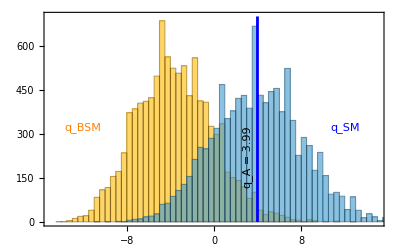

```mathematica
(*Figure 14*)
Show[Histogram[{qBSM,qSM},{0.5},Frame->True,PlotRange->{{-15,15},{All,All}}],
ParametricPlot[{qA,u},{u,0,700},PlotStyle->Blue],
Epilog->{
Text["q_A = 3.99",{3.1,220},{0,0},{0,1}],
Text[Style["q_SM",Blue],{12,320},{0,0},{1,0}],
Text[Style["q_BSM",Orange],{-12,320},{0,0},{1,0}]}]
```

```mathematica
(*4.67*)
qA = qo3[A]
```

3.98901

```mathematica
(*4.68*)
Count[qBSM,_?(Between[{qA,∞}])]
(*4.69*)
Count[qBSM,_?(Between[{qA,∞}])]/NMC//N
```

230

0.023

Wilks’ Theorem

```mathematica
(*4.70*)
H[μ_]:=μ HBSM + (1-μ)HSM
```

```mathematica
(*4.72*)
Timing[Monitor[
qBSM=Table[FindMaximum[{-2Sum[drawsBSM[[j]][[i]]Log[(HBSM[[i]]/(H[μ][[i]]))],{i,1,Length[HBSM]}]//N,0<=μ<=1},μ,PrecisionGoal->3][[1]],{j,1,NMC}];
,{j}]]
```

{66.2375,Null}

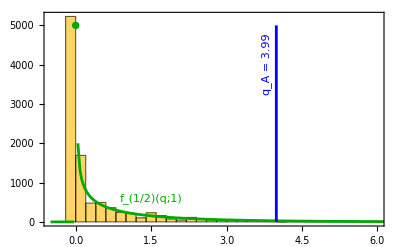

```mathematica
(*Figure 15*)
Show[
Histogram[{qBSM},{0.2}],
Plot[{NMC/(2*5) PDF[ChiSquareDistribution[1],x]},{x,-0.5,100},PlotRange->{0,NMC/5},PlotStyle->Darker@Green],

ListPlot[{{0,5000}},PlotStyle->Darker@Green],
ParametricPlot[{qo3[A],u},{u,0,NMC/2},PlotStyle->Blue],
Frame->True,PlotRange->{{-0.5,6},{All,All}},
Epilog->{
Text[Style["q_A = 3.99",Blue],{3.8,4000},{0,0},{0,1}],
Text[Style["f_(1/2)(q;1)",Darker@Green],{1.5,600},{0,0},{1,-0.4}]}]
```

```mathematica
(*4.75*)
qA = -2Sum[A⟦i⟧Log[HBSM⟦i⟧/A[[i]]],{i,1,Length[HBSM]}]//N
```

3.98901

```mathematica
(*4.76*)
Count[qBSM,_?(Between[{qA,∞}])]
(*4.77*)
Count[qBSM,_?(Between[{qA,∞}])]/NMC//N
```

198

0.0198

Asymptotic Distribution of the Test Statistic

```mathematica
(*4.80*)
1/2 Erfc[Sqrt[qA/2]]
```

0.0228989

Asymptotic Limit of the Test Statistic of the Asimov Data Set

```mathematica
(*4.88*)
χ2[HBSM,A]
```

4.54945

```mathematica
(*4.92*)
1/2 Erfc[√(χ2[HBSM,A]/2)]
```

0.0164647

### 4.3 Realistic Hawking Radiation from a Black Hole Explosion

```mathematica
(*4.93*)
HSM={0.853,2.42,6.40,15.5,33.2,60.9,89.9,101,15.4};
```

```mathematica
(*4.94*)
HBSM={0.840,2.34,6.02,14.1,29.1,51.0,80.9,121,20.7};
```

```mathematica
toSteps[d_] := Flatten[
   Table[{{d[[i - 1, 1]], d[[i, 2]]}, {d[[i, 1]], d[[i, 2]]}}, {i, 2, Length[d]}], 1];
```

```mathematica
logTicks[lbl_] := Join[
   Table[{10.^k, If[lbl, Superscript[10, k], ""], {0.025, 0}}, {k, -5, 4}],
   Flatten[Table[{m 10.^k, "", {0.012, 0}}, {k, -5, 3}, {m, 2, 9}], 1]];
```

```mathematica
yTicks[lbl_] := Join[
   Table[{y, If[lbl, y, ""], {0.025, 0}}, {y, 0, 140, 20}],
   Table[{y, "", {0.012, 0}}, {y, Complement[Range[0, 145, 5], Range[0, 140, 20]]}]];
```

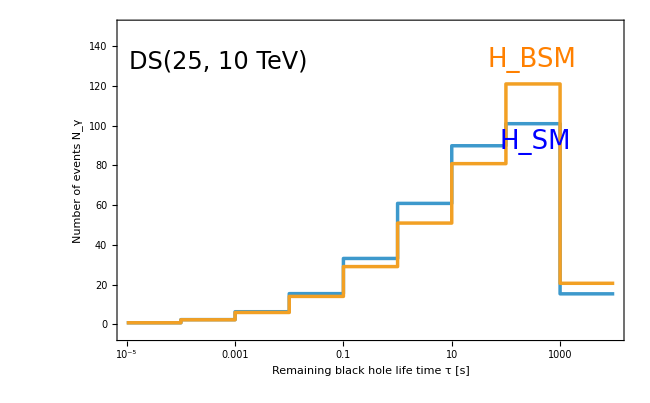

```mathematica
(*Figure 16*)
ListLogLinearPlot[
 {toSteps[Transpose[{Table[10^x,{x,-5,4}],Join[{0},HSM]}]], toSteps[Transpose[{Table[10^x,{x,-5,4}],Join[{0},HBSM]}]]},
 Joined -> True,
 PlotStyle -> { AbsoluteThickness[2.5], AbsoluteThickness[2.5]},
 PlotRange -> {{10^-5, 10^4}, {-5, 150}},
 Frame -> True,FrameTicks -> {{yTicks[True], yTicks[False]}, {logTicks[True], logTicks[False]}},
 FrameStyle -> Directive[Black, AbsoluteThickness[1]],
 FrameLabel -> {"Remaining black hole life time τ [s]","Number of events N_γ"},
 Epilog -> {
   Text[Style["H_BSM",Orange, 26], {Log[300], 133}],
   Text[Style["H_SM", Blue, 26], {Log[350], 92}],
   Text[Style["DS(25, 10 TeV)", 24],Scaled[{0.2, 0.87}]]},
 BaseStyle -> {FontFamily -> "Times", FontSize -> 22},AspectRatio -> 0.62,ImageSize -> 650]
```

```mathematica
(*4.95*)
A=HSM;
```

```mathematica
NMC=10000;
```

```mathematica
Ntotal=Round[Total[HBSM]];
```

```mathematica
qo2[o_]:=-2Log[Product[(HBSM[[i]]/Ntotal)^o[[i]]/(HBSM[[i]]/Ntotal)^HBSM[[i]] (HBSM[[i]]!)/(o[[i]]!),{i,1,Length[HBSM]}]]//N
```

```mathematica
drawsBSM=Table[RandomVariate[MultinomialDistribution[Ntotal,HBSM/Ntotal]],{i,1,NMC}];
```

```mathematica
qTableMC=Table[qo2[drawsBSM[[i]]],{i,1,NMC}];
```

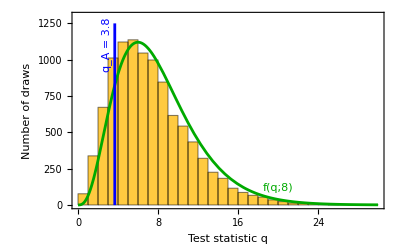

```mathematica
(*Figure 17 left*)
Show[
Histogram[qTableMC,{1},Frame->True,FrameLabel->{"Test statistic q","Number of draws"},PlotRange->{{0,30},{0,1300}}],
Plot[NMC PDF[ChiSquareDistribution[Length[HBSM]-1],x],{x,0,30},PlotStyle->Darker@Green],
ParametricPlot[{qo2[A],u},{u,-1,1250},PlotStyle->Blue],
Epilog->{
Text[Style["q_A = 3.8",Blue],{2.9,1100},{0,0},{0,1}],
Text[Style["f(q;8)",Darker@Green],{20,120},{0,0},{1,0}]}]
```

```mathematica
H[μ_]:=μ HBSM + (1-μ)HSM
```

```mathematica
Timing[Monitor[
qBSM=Table[FindMaximum[{-2Sum[drawsBSM[[j]][[i]]Log[(HBSM[[i]]/(H[μ][[i]]))],{i,1,Length[HBSM]}]//N,0<=μ<=1},μ,PrecisionGoal->3][[1]],{j,1,NMC}];
,{j}]]
```

{82.8695,Null}

```mathematica
qo3[o_]:=-2Sum[o[[i]]Log[HBSM[[i]]/HSM[[i]]],{i,1,Length[HBSM]}]//N
```

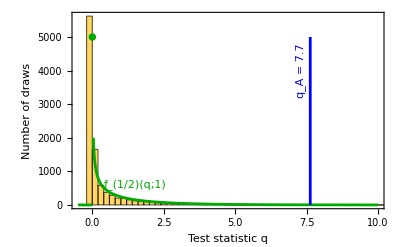

```mathematica
(*Figure 17 right*)
Show[
Histogram[{qBSM},{0.2},FrameLabel->{"Test statistic q","Number of draws"}],
Plot[{NMC/(2*5) PDF[ChiSquareDistribution[1],x]},{x,-0.5,10},PlotRange->{0,NMC/5},PlotStyle->Darker@Green],

ListPlot[{{0,5000}},PlotStyle->Darker@Green],
ParametricPlot[{qo3[A],u},{u,0,NMC/2},PlotStyle->Blue],
Frame->True,PlotRange->{{-0.5,10},{All,All}},
Epilog->{
Text[Style["q_A = 7.7",Blue],{7.3,4000},{0,0},{0,1}],
Text[Style["f_(1/2)(q;1)",Darker@Green],{1.5,600},{0,0},{1,-0.4}]}]
```

## 7 Systematic Errors

```mathematica
(* Please run this cell before beginning this section so that variables are not inadvertantly stored from previous sections *)
Quit[];
```

```mathematica
σ={{σS,0,0},{0,σT,0},{0,0,σU}};
ρ={{ρSS,ρST,ρSU},{ρST,ρTT,ρTU},{ρSU,ρTU,ρUU}};
```

```mathematica
replacements={σS->0.0064,σT->0.0079,σU->0.0054,ρSS->1,ρST->0.92,ρSU->-0.67,ρTT->1,ρTU->-0.88,ρUU->1};
```

```mathematica
V=σ.ρ.σ
```

{{ρSS σS^2,ρST σS σT,ρSU σS σU},{ρST σS σT,ρTT σT^2,ρTU σT σU},{ρSU σS σU,ρTU σT σU,ρUU σU^2}}

```mathematica
HBSM1={0.002,0.002,0};
HBSM2={0.002,-0.002,0};
```

```mathematica
VInv=Inverse[V]/.replacements;
```

```mathematica
(*7.10*)
HBSM1.VInv.HBSM1
```

0.33461

```mathematica
(*7.11*)
HBSM2.VInv.HBSM2
```

7.22969